## Verify and Plot

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

myVerify [varSet_,flowVec_,initBoundary_,unsafeBoundary_,bc_,deg_]:= Module[
{lambda,unsafeCons,initCons,bcLie,bc1,bc2,bc3,bc4,timev},
timev=Now;
lambda = -1;
unsafeCons = And@@(GreaterEqual[#,0]&/@unsafeBoundary);
initCons = And@@(GreaterEqual[#,0]&/@initBoundary);
bcLie =D[bc,varSet[[1]]]*flowVec[[1]]+D[bc,varSet[[2]]]*flowVec[[2]];
bc1 = FindInstance[bc>0&&initCons,varSet];
bc2 =FindInstance[bc≤ 0&&unsafeCons,varSet];
bc3 =FindInstance[bcLie-lambda*bc> 0,varSet];
bc4 =FindInstance[bc== 0&&bcLie> 0,varSet];
(*Print["deg: ",deg, "  ",bc1,bc2,bc3,bc4];*)
If[Or[Length[bc1]+Length[bc2]+Length[bc3]==0,Length[bc1]+Length[bc2]+Length[bc4]==0],
Return[1],
Return[0]];
]

verifyResults[benchmark_,plot_,plotRange_,verifyTime_]:= Module[
{systemPath,varSet,flowVec,initCons,unsafeCons,bcPath,bcData,ebc,hbc,ebcDeg,hbcDeg,totaltime,totalsdptime,time,etime,htime,ptime,result,i},
systemPath=FileNameJoin[{".","Results","systems",StringJoin[benchmark,".txt"]}];
{varSet,flowVec,initCons,unsafeCons} = ReadList[systemPath];
ebcDeg=0;
hbcDeg=0;
Print["Variables: ",varSet];
Print["Flow: ",flowVec];
Print["Initial: ",initCons];
Print["Unsafe: ",unsafeCons];

Print["Verifying SUFFICIENT condition results..."];
bcPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ Length[bcData],i++,
ebc = bcData[[i]][[1]];
time = bcData[[i]][[2]];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,ebc,i],verifyTime,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime + result[[1]];
If[result[[2]]== 1,
ebcDeg=i;
Print["Verified."];
Print[ebc];
Break[]
];
If[result[[2]]== 2,
ebcDeg=i;
Print["Verify out of time."];
Print[ebc];
Break[]
];
];
etime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[ebcDeg>0,
Print["Sufficient Condition: Verified. time used: ",etime];,
Print["Sufficient Condition: No valid soltion, time used: ",etime];
];

Print["Verifying Necessary results..."];
bcPath=FileNameJoin[{".","Results","necessary",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ Length[bcData],i++,
hbc = bcData[[i]][[1]];
time =bcData[[i]][[2]];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,hbc,i],verifyTime,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime + result[[1]];
If[result[[2]]== 1,
hbcDeg=i;
Print["Verified."];
Print[hbc];
Break[]
];
If[result[[2]]== 2,
hbcDeg=i;
Print["Verify out of time."];
Print[hbc];
Break[]
];
];
htime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[hbcDeg>0,
Print["Necessary condition: verified. time used: ",htime];,
Print["Necessary condition: No valid soltion, time used: ",htime];
];
If[ plot== 1,
If[Length[varSet]== 2,myPlot2D[varSet,plotRange,flowVec,unsafeCons,initCons,If[ebcDeg== 0,1,ebc],If[hbcDeg== 0,1,hbc]]];
If[Length[varSet]== 3,myPlot3D[varSet,plotRange,flowVec,unsafeCons,initCons,If[ebcDeg== 0,1,ebc],If[hbcDeg== 0,1,hbc]]];
]
]
myPlot2D [varSet_,varRange_,flowVec_,unsafeBoundary_,initBoundary_,bc_,bch_]:= Module[
{ranges,flowPlot,initCons,unsafeCons,initPlot,unsafePlot,initSamples,flow,trajGen,trajTable,trajPlot,sampleNum,solution,trajPlotAll,bcPlot,bchPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];
flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];
initCons=And@@Thread[GreaterEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[GreaterEqualThan[0][unsafeBoundary]];
initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
sampleNum = 5;
initSamples=RandomPoint[ImplicitRegion[initCons&&varRange[[1]][[1]]≤ varSet[[1]]≤ varRange[[1]][[2]]&& varRange[[2]][[1]]≤ varSet[[2]]≤ varRange[[2]][[2]],varSet],sampleNum];
Off[NDSolve::ndsz];
solution[s0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==s0]],varSet,{t,0,20},Method->"StiffnessSwitching"];trajPlot=ParametricPlot[Evaluate[(#[t]&/@varSet)/.solution[#]&/@initSamples],{t,0,20},PlotStyle->Directive[Black,Thickness[Large]]];
bcPlot=RegionPlot[bc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
bchPlot=RegionPlot[bch≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[flowPlot,initPlot,unsafePlot,trajPlot,bcPlot,bchPlot, FrameLabel->varSet]]
]

myPlot3D [varSet_,varRange_,flowVec_,unsafeBoundary_,initBoundary_,bc_,bch_]:= Module[
{ranges,flowPlot,initCons,unsafeCons,initPlot,unsafePlot,initSamples,flow,trajGen,trajTable,trajPlot,sampleNum,solution,trajPlotAll,bcPlot,bchPlot},
Print["Plot3d..."];
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];
(*flowPlot =VectorPlot3D[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->{Opacity[0.4],Gray}];*)
(*plot init and unsafe regions*)
initCons=And@@Thread[GreaterEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[GreaterEqualThan[0][unsafeBoundary]];
initPlot=RegionPlot3D[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100,Mesh->None];
unsafePlot=RegionPlot3D[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100,Mesh->None];
(*plot sample trajectories*)
sampleNum = 5;
initSamples=RandomPoint[ImplicitRegion[initCons&&varRange[[1]][[1]]≤ varSet[[1]]≤ varRange[[1]][[2]]&& varRange[[2]][[1]]≤ varSet[[2]]≤ varRange[[2]][[2]]&&varRange[[3]][[1]]≤ varSet[[3]]≤ varRange[[3]][[2]],varSet],sampleNum];
Off[NDSolve::ndsz];
solution[s0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==s0]],varSet,{t,0,20},Method->"StiffnessSwitching"];trajPlot=ParametricPlot3D[Evaluate[(#[t]&/@varSet)/.solution[#]&/@initSamples],{t,0,20},PlotStyle->Directive[Black,Thickness[Large]]];
bcPlot=RegionPlot3D[bc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.3],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100,Mesh->None];
bchPlot=RegionPlot3D[bch≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.3],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100,Mesh->None];
Print[Show[initPlot,unsafePlot,trajPlot,bcPlot,bchPlot, FrameLabel->varSet]]
];
```

```mathematica
Plot3D
```

## Benchmarks

### 2-dim benchmarks

vector-1

Variables: {x1,x2}

Flow: {x2,x1}

Initial: {4+x1,4+x2,-x1,-x2}

Unsafe: {-6-4 x1-x1^2+4 x2-x2^2}

Verifying SUFFICIENT condition results...

Verified.

-3.96809-0.83199 x1-1.02151 x1^2+5.59506 x2-4.43124 x1 x2-0.784137 x2^2

totalsdptime: 0.048713

Sufficient Condition: Verified. time used: 4.34156

Verifying Necessary results...

Verified.

-6.2187-2.37678 x1-0.807431 x1^2+5.22439 x2-3.03217 x1 x2-0.0184872 x2^2

totalsdptime: 0.028743

Necessary condition: verified. time used: 0.244061

Plot2d...

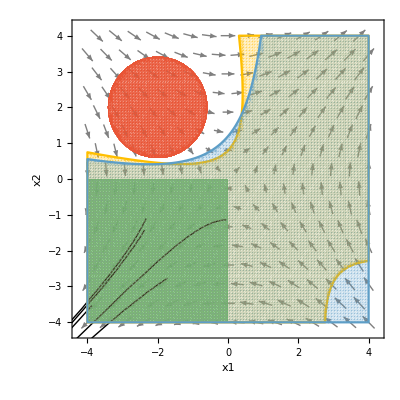

vector-2

Variables: {x1,x2}

Flow: {x2,x1}

Initial: {-1+x1 x2}

Unsafe: {-2-x1,-2+x2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.003663

Sufficient Condition: No valid soltion, time used: 0.0161197

Verifying Necessary results...

totalsdptime: 0.017352

Necessary condition: No valid soltion, time used: 0.0922415

Plot2d...

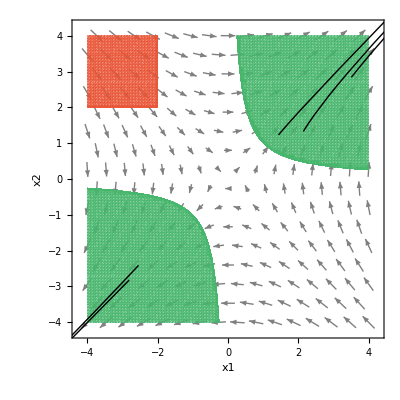

barrier-1

Variables: {x1,x2}

Flow: {x2,-x1+0.333333 x1^3-x2}

Initial: {-2.+3. x1-x1^2-x2^2}

Unsafe: {-1.84-2. x1-x1^2-2. x2-x2^2}

Verifying SUFFICIENT condition results...

Verified.

-1.75784-1.59531 x1-0.414108 x1^2-2.28573 x2-1.1039 x1 x2

totalsdptime: 0.024236

Sufficient Condition: Verified. time used: 0.0421679

Verifying Necessary results...

Divide::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-4.770948308081848 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-5.349863045582899 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

totalsdptime: 0.986998

Necessary condition: No valid soltion, time used: 1.15907

Plot2d...

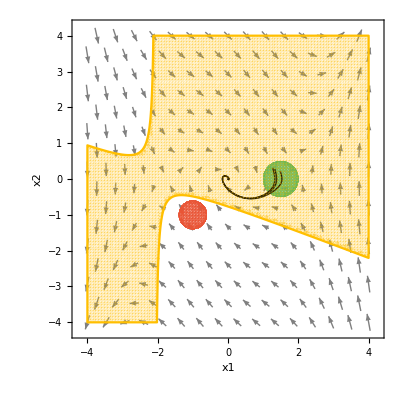

barrier-2

Variables: {x1,x2}

Flow: {x2,-x1+0.333333 x1^3-x2}

Initial: {-1.+x1 x2,x1}

Unsafe: {-2.-x1,-2.+x2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.005721

Sufficient Condition: No valid soltion, time used: 0.0212995

Verifying Necessary results...

totalsdptime: 0.981283

Necessary condition: No valid soltion, time used: 1.15972

Plot2d...

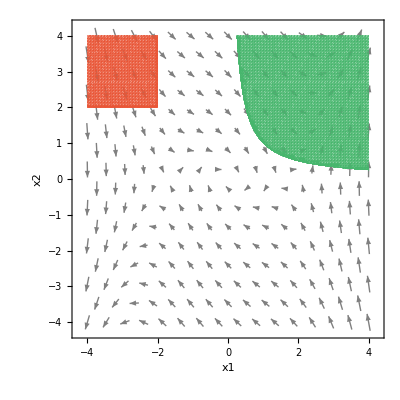

lie-der-1

Variables: {x1,x2}

Flow: {-2. x2,x1^2}

Initial: {-0.84-2. x1-x1^2-x2^2}

Unsafe: {-0.84-x1^2-2. x2-x2^2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.004118

Sufficient Condition: No valid soltion, time used: 0.0231395

Verifying Necessary results...

totalsdptime: 0.008851

Necessary condition: No valid soltion, time used: 0.0709939

Plot2d...

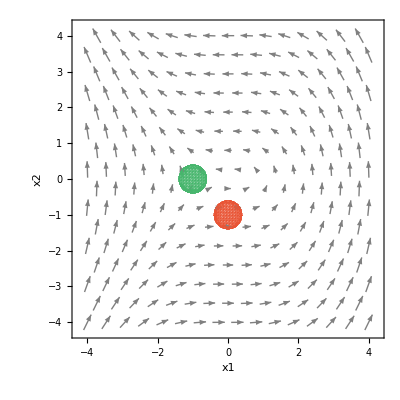

lie-der-2

Variables: {x1,x2}

Flow: {-2. x2,x1^2}

Initial: {1.-x2^2,-1.-x1}

Unsafe: {-2.+x1-0.04 x2^2,x1}

Verifying SUFFICIENT condition results...

Verified.

-3.971+1.01568 x1-0.354212 x1^2+0.464874 x1^3-2.27353 x2+1.35759 x1 x2-0.313692 x1^2 x2+1.46411 x2^2-0.0518153 x1 x2^2-0.103631 x2^3

totalsdptime: 1.0467

Sufficient Condition: Verified. time used: 1.06288

Verifying Necessary results...

Verified.

-8.55264+2.13079 x1-0.512443 x1^2+0.879336 x1^3-5.00239 x2+2.78831 x1 x2-0.61001 x1^2 x2+2.8781 x2^2-0.102482 x1 x2^2-0.204964 x2^3

totalsdptime: 0.871964

Necessary condition: verified. time used: 1.06392

Plot2d...

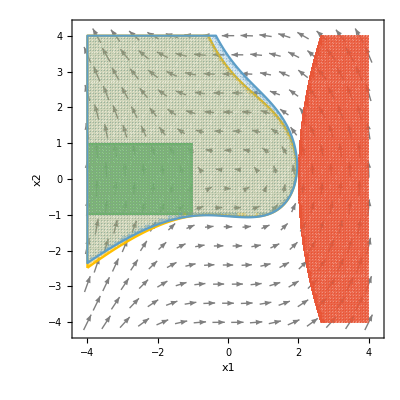

arch1-1

Variables: {x1,x2}

Flow: {-x1+2. x1^3 x2^2,-x2}

Initial: {-3.75-x1^2+4. x2-x2^2}

Unsafe: {-16.59-6. x1-x1^2+5.6 x2-x2^2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.004317

Sufficient Condition: No valid soltion, time used: 0.102999

Verifying Necessary results...

Divide::infy: Infinite expression 1/(0``-24.010273900191766) encountered.

Verified.

-1.06776×10^7+162417. x1-10152.5 x1^2+812.773 x1^3-134.576 x1^4+5.62428×10^6 x2-63933.9 x1 x2+38748.1 x1^2 x2-4622.67 x1^3 x2+2.22909×10^6 x2^2-190560. x1 x2^2-65946.5 x1^2 x2^2-2.44132×10^6 x2^3+33.9082 x1 x2^3+531224. x2^4

totalsdptime: 2.39733

Necessary condition: verified. time used: 3.14095

Plot2d...

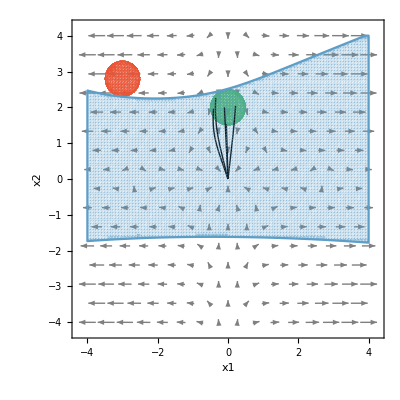

arch1-2

Variables: {x1,x2}

Flow: {-x1+2 x1^3 x2^2,-x2}

Initial: {1-x1^2,-2+x2}

Unsafe: {1-x1^2,-2-x2}

Verifying SUFFICIENT condition results...

Verified.

-1.12206-1.67957 x2

totalsdptime: 0.006154

Sufficient Condition: Verified. time used: 0.0141722

Verifying Necessary results...

totalsdptime: 0.300022

Necessary condition: No valid soltion, time used: 0.408255

Plot2d...

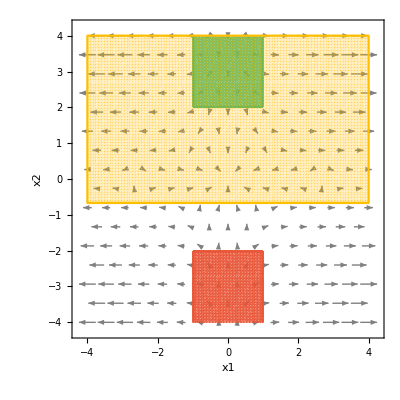

arch2-1

Variables: {x1,x2}

Flow: {-1.+x1^2+x2^2,-5.+5. x1 x2}

Initial: {-1.75-x1^2+4. x2-x2^2}

Unsafe: {-1.-x1,3.+x1,-2.-x2,3.+x2}

Verifying SUFFICIENT condition results...

Verified.

-5.22216-1.38858 x1-0.208757 x1^2-0.578261 x1^3+0.0214286 x2-0.202339 x1 x2-0.652228 x1^2 x2-0.0718918 x2^2-0.782459 x1 x2^2-0.217988 x2^3

totalsdptime: 0.82803

Sufficient Condition: Verified. time used: 0.855196

Verifying Necessary results...

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Verified.

-7.94188-2.69714 x1-1.02493 x1^2-0.951145 x1^3+0.179292 x2+0.263228 x1 x2-0.49943 x1^2 x2+0.00132236 x2^2-0.971081 x1 x2^2-0.253219 x2^3

totalsdptime: 0.851101

Necessary condition: verified. time used: 0.920646

Plot2d...

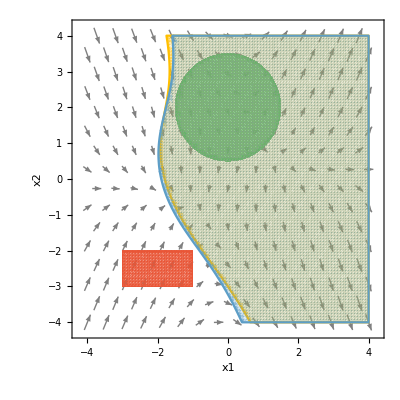

arch2-2

Variables: {x1,x2}

Flow: {-1+x1^2+x2^2,-5+5 x1 x2}

Initial: {-2+x1,-2-x2}

Unsafe: {-1-x1^2+x2,x2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.004747

Sufficient Condition: No valid soltion, time used: 0.0134227

Verifying Necessary results...

Verified.

0.0000138493-0.000047008 x1+0.0000206982 x2

totalsdptime: 0.008305

Necessary condition: verified. time used: 0.0440226

Plot2d...

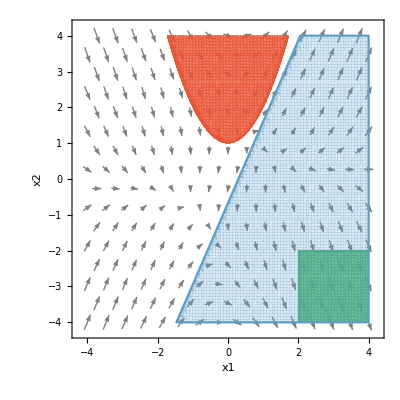

arch3-1

Variables: {x1,x2}

Flow: {x1-x1^3+x2-x1 x2^2,-x1+x2-x1^2 x2-x2^3}

Initial: {0.04-x1^2-x2^2}

Unsafe: {-12.25+5. x1-x1^2+5. x2-x2^2}

Verifying SUFFICIENT condition results...

Verified.

-2.47438+0.0981382 x1+0.680066 x1^2+0.143792 x2+0.357087 x1 x2+0.671213 x2^2

totalsdptime: 0.911395

Sufficient Condition: Verified. time used: 0.921846

Verifying Necessary results...

Verified.

-6.18087+0.571858 x1+1.52979 x1^2+0.608802 x2+0.265804 x1 x2+1.50934 x2^2

totalsdptime: 1.10876

Necessary condition: verified. time used: 1.1458

Plot2d...

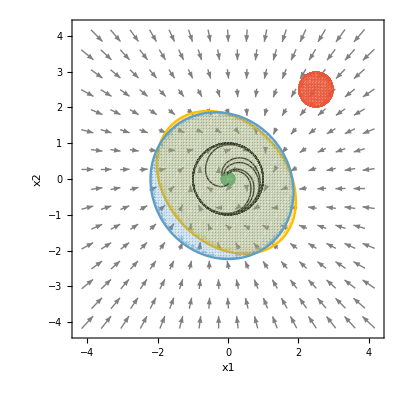

arch3-2

Variables: {x1,x2}

Flow: {x1-x1^3+x2-x1 x2^2,-x1+x2-x1^2 x2-x2^3}

Initial: {-2+x1-x2^2,x2,x1}

Unsafe: {-2-x1^2-x2,-x2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.004617

Sufficient Condition: No valid soltion, time used: 0.0136487

Verifying Necessary results...

totalsdptime: 0.011547

Necessary condition: No valid soltion, time used: 0.0620442

Plot2d...

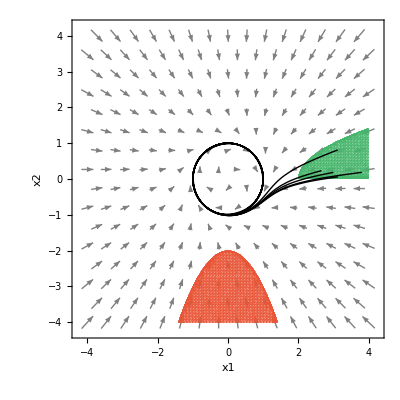

arch4-1

Variables: {x1,x2}

Flow: {-2. x1+x1^2+x2,x1-2. x2+x2^2}

Initial: {0.01-x1^2-x2^2}

Unsafe: {-1.0625+1.5 x1-x1^2+1.5 x2-x2^2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.004683

Sufficient Condition: No valid soltion, time used: 0.017476

Verifying Necessary results...

Verified.

-0.0000286904+0.0000318505 x1+0.000105571 x1^2-0.0000449422 x1^3+0.0000318423 x2-0.000201192 x1 x2+0.0000496817 x1^2 x2+0.000105563 x2^2+0.0000496487 x1 x2^2-0.0000449104 x2^3

totalsdptime: 0.835189

Necessary condition: verified. time used: 0.903025

Plot2d...

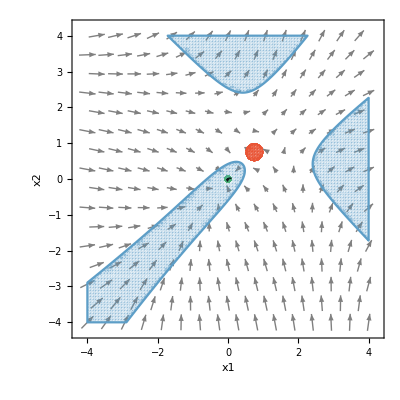

arch4-2

Variables: {x1,x2}

Flow: {-2. x1+x1^2+x2,x1-2. x2+x2^2}

Initial: {0.25-x1^2-x2^2}

Unsafe: {-4.+x1 x2,-x1}

Verifying SUFFICIENT condition results...

totalsdptime: 0.004488

Sufficient Condition: No valid soltion, time used: 0.0150217

Verifying Necessary results...

totalsdptime: 0.018375

Necessary condition: No valid soltion, time used: 0.17279

Plot2d...

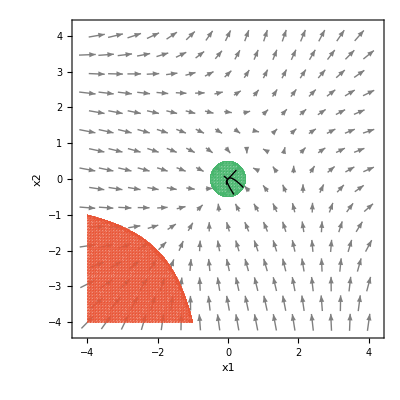

nagumo-1

Variables: {x1,x2}

Flow: {0.875+x1-0.333333 x1^3-x2,0.056+0.08 x1-0.064 x2}

Initial: {-2.0625-1.5 x1-x1^2+2.5 x2-x2^2}

Unsafe: {-8.0625-4.5 x1-x1^2-3.5 x2-x2^2}

Verifying SUFFICIENT condition results...

Verified.

-2.10682-0.953505 x1+0.22877 x1^2-1.66948 x2-0.555923 x2^2

totalsdptime: 0.01463

Sufficient Condition: Verified. time used: 0.0278298

Verifying Necessary results...

Verified.

-6.41488-2.64924 x1+0.754256 x1^2-4.541 x2-0.000575162 x1 x2-1.47273 x2^2

totalsdptime: 0.913686

Necessary condition: verified. time used: 1.1007

Plot2d...

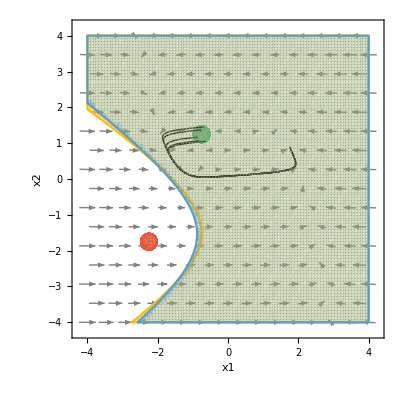

nagumo-2

Variables: {x1,x2}

Flow: {0.875+x1-0.333333 x1^3-x2,0.056+0.08 x1-0.064 x2}

Initial: {-2.0625-1.5 x1-x1^2+2.5 x2-x2^2}

Unsafe: {-2.-x2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.005265

Sufficient Condition: No valid soltion, time used: 0.0401848

Verifying Necessary results...

Verified.

-10.6194+5.67176 x1+5.7601 x1^2-7.41702 x1^3+2.10241 x1^4-44.9347 x2+27.9835 x1 x2-3.26525 x1^2 x2+0.138954 x1^3 x2+3.15423 x2^2-0.591916 x1 x2^2+0.0883259 x1^2 x2^2+0.0720022 x2^3+0.0297173 x1 x2^3+0.0074228 x2^4

totalsdptime: 2.40875

Necessary condition: verified. time used: 2.66892

Plot2d...

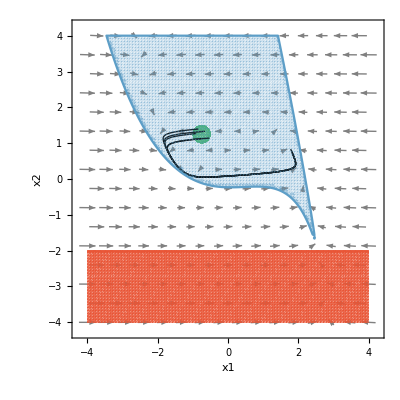

```mathematica
benchmarks={"vector-1","vector-2","barrier-1","barrier-2","lie-der-1","lie-der-2","arch1-1","arch1-2","arch2-1","arch2-2","arch3-1","arch3-2","arch4-1","arch4-2","nagumo-1","nagumo-2"};
For[i=1,i≤ 16,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
verifytime=10;
plot =1;
plotRange = {{-4,4},{-4,4}};
verifyResults[benchmarkname,1plot,plotRange,verifytime];
]
```

```mathematica
benchmarks={"lorenz-1","lorenz-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
verifytime=10;
plot =1;
plotRange = {{-20,20},{-20,20},{-20,20}};
verifyResults[benchmarkname,1plot,plotRange,verifytime];
]
```

lorenz-1

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-575.75-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-487.75-33. x1-x1^2-29. x2-x2^2+5. x3-x3^2}

Verifying SUFFICIENT condition results...

Verify out of time.

-2.44203×10^8-42721. x1+1.19419×10^6 x1^2-195.128 x1^3+1404.7 x1^4-1668.48 x2-348605. x1 x2-245.919 x1^2 x2+12.9349 x1^3 x2+947870. x2^2-39.2557 x1 x2^2+40.3085 x1^2 x2^2+0.0099434 x1^3 x2^2+1.30994 x2^3+6.73285 x1 x2^3-0.0150082 x1^2 x2^3+740.944 x2^4-6.11762×10^7 x3+8146.89 x1 x3-11615.9 x1^2 x3+4.29249 x1^3 x3+2199.12 x2 x3+9284.27 x1 x2 x3-1.7553 x1^2 x2 x3+1.00518 x1^3 x2 x3-89472.3 x2^2 x3-1.83737 x1 x2^2 x3-3.08343 x1^2 x2^2 x3+0.359282 x2^3 x3+3.27846×10^6 x3^2-112.877 x1 x3^2-189.724 x1^2 x3^2+0.0253822 x1^3 x3^2+13.7248 x2 x3^2-0.985021 x1 x2 x3^2+0.000633035 x1^2 x2 x3^2+1559.87 x2^2 x3^2-85885.7 x3^3-1.60733 x1 x3^3-7.78257 x1^2 x3^3+0.136136 x2 x3^3+818.902 x3^4

totalsdptime: 10.566

Sufficient Condition: Verified. time used: 10.7498

Verifying Necessary results...

Verify out of time.

-3.00481×10^8-5.33446×10^7 x1+2.71008×10^7 x1^2+19058.5 x1^3+123326. x1^4+111.018 x1^5-5.89577×10^7 x2-3.26705×10^7 x1 x2-45853.1 x1^2 x2+29468.2 x1^3 x2+154.072 x1^4 x2-3.02088×10^7 x2^2-621618. x1 x2^2+118711. x1^2 x2^2+599.265 x1^3 x2^2-738444. x2^3-7271.86 x1 x2^3+161.228 x1^2 x2^3+3073.82 x2^4+90.3249 x1 x2^4+67.0244 x2^5-3.25386×10^8 x3+7.30657×10^7 x1 x3-5.33453×10^6 x1^2 x3-21757.5 x1^3 x3-554.579 x1^4 x3+7.18621×10^7 x2 x3-976593. x1 x2 x3+5413.46 x1^2 x2 x3+151.477 x1^3 x2 x3-1.52058×10^6 x2^2 x3-40114.1 x1 x2^2 x3+249.187 x1^2 x2^2 x3-11369.2 x2^3 x3+116.808 x1 x2^3 x3+122.345 x2^4 x3+6.48771×10^7 x3^2-615445. x1 x3^2+125873. x1^2 x3^2+605.972 x1^3 x3^2-291361. x2 x3^2-20525.8 x1 x2 x3^2+176.087 x1^2 x2 x3^2-1623.83 x2^2 x3^2+190.347 x1 x2^2 x3^2+227.209 x2^3 x3^2-1.54748×10^6 x3^3-35551.5 x1 x3^3+190.594 x1^2 x3^3-14103.4 x2 x3^3+70.4779 x1 x2 x3^3+411.374 x2^2 x3^3-6653.51 x3^4+25.8707 x1 x3^4+153.159 x2 x3^4+333.185 x3^5

totalsdptime: 10.6588

Necessary condition: verified. time used: 12.9707

Plot3d...

-Graphics3D-

lorenz-2

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-575.75-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-4.-0.01 x1^2-0.01 x2^2-x3,-x3}

Verifying SUFFICIENT condition results...

totalsdptime: 0.011598

Sufficient Condition: No valid soltion, time used: 0.023029

Verifying Necessary results...

Verified.

-0.0000695144-0.0000200022 x3

totalsdptime: 0.015332

Necessary condition: verified. time used: 0.0987984

Plot3d...

-Graphics3D-

```mathematica
benchmarks={"lotka-1","lotka-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
verifytime=10;
plot =1;
plotRange = {{-4,4},{-4,4},{-4,4}};
verifyResults[benchmarkname,1plot,plotRange,verifytime];
]
```

lotka-1

Variables: {x1,x2,x3}

Flow: {x1-x1 x3,x2-2. x2 x3,-x3+x1 x3+x2 x3}

Initial: {-4.16+2. x1-x1^2+2. x2-x2^2+3. x3-x3^2}

Unsafe: {-4.16-2. x1-x1^2-2. x2-x2^2-3. x3-x3^2}

Verifying SUFFICIENT condition results...

totalsdptime: 0.006231

Sufficient Condition: No valid soltion, time used: 0.274802

Verifying Necessary results...

Verify out of time.

-1602.89-348.561 x1-92.4198 x1^2+8.30539 x1^3-0.245346 x1^4+0.00254841 x1^5-369.507 x2-72.1035 x1 x2+11.8344 x1^2 x2-0.418624 x1^3 x2+0.0031645 x1^4 x2-22.2912 x2^2+9.7088 x1 x2^2-0.432019 x1^2 x2^2+0.00248361 x1^3 x2^2+4.20175 x2^3-0.400185 x1 x2^3+0.00485405 x1^2 x2^3-0.170579 x2^4+0.00511816 x1 x2^4+0.00212415 x2^5-886.791 x3-5.8392 x1 x3+17.4082 x1^2 x3-0.934713 x1^3 x3+0.0138908 x1^4 x3-20.2581 x2 x3+17.957 x1 x2 x3-1.02261 x1^2 x2 x3+0.00321843 x1^3 x2 x3+22.0702 x2^2 x3-1.3761 x1 x2^2 x3+0.0133642 x1^2 x2^2 x3-1.3514 x2^3 x3+0.0207524 x1 x2^3 x3+0.0217125 x2^4 x3+95.9742 x3^2-18.5619 x1 x3^2+0.418382 x1^2 x3^2-0.00891048 x1^3 x3^2-5.55634 x2 x3^2+0.407989 x1 x2 x3^2-0.0238402 x1^2 x2 x3^2-1.24897 x2^2 x3^2+0.00977267 x1 x2^2 x3^2+0.0370256 x2^3 x3^2-10.5596 x3^3+1.53381 x1 x3^3-0.0366244 x1^2 x3^3+0.718716 x2 x3^3-0.0450645 x1 x2 x3^3+0.0246076 x2^2 x3^3+0.458142 x3^4-0.0293234 x1 x3^4-0.0168382 x2 x3^4-0.00647808 x3^5

totalsdptime: 10.9293

Necessary condition: verified. time used: 14.3197

Plot3d...

-Graphics3D-

lotka-2

Variables: {x1,x2,x3}

Flow: {x1-x1 x3,x2-2. x2 x3,-x3+x1 x3+x2 x3}

Initial: {-2.91+2. x1-x1^2+2. x2-x2^2-2. x3-x3^2}

Unsafe: {-0.5-0.01 x1^2-0.01 x2^2+x3}

Verifying SUFFICIENT condition results...

totalsdptime: 0.003856

Sufficient Condition: No valid soltion, time used: 0.01506

Verifying Necessary results...

Verified.

0.0000100003 x3

totalsdptime: 0.007386

Necessary condition: verified. time used: 0.0738911

Plot3d...

-Graphics3D-

```mathematica
benchmarks={"lyapunov-1","lyapunov-2"};
For[i=1,i≤ 2,i++,
benchmarkname = benchmarks[[i]];
Print[benchmarkname];
verifytime=10;
plot =1;
plotRange = {{-4,4},{-4,4},{-4,4}};
verifyResults[benchmarkname,1plot,plotRange,verifytime];
]
```